```mathematica
psi[x_] := A * Sin[k * x]
```

```mathematica
Solve[Integrate[psi[x]^2, {x, 0, rA}] == 1, A]
```

{{A→-2/(√(2 rA-Sin[2 k rA]/k))},{A→2/(√(2 rA-Sin[2 k rA]/k))}}

```mathematica
A = 2/(√(2 rA-Sin[2 k rA]/k))
```

2/(√(2 rA-Sin[2 k rA]/k))

```mathematica
psi[rA]^2
```

```mathematica
(4 Sin[k rA]^2)/(2 rA-Sin[2 k rA]/k)
```

```mathematica
f[k_, a_] := (4 Sin[k a]^2)/(2 a-Sin[2 k a]/k)
```

```mathematica
Plot3D[f[k, a], {k, Pi / 2 - 0.5, Pi / 2 + 0.5}, {a, 1, 10}, ImageSize->Large, Ticks->{Range[-10 * Pi, 10 * Pi, Pi / 2],Automatic, Automatic}]
```

-Graphics3D-

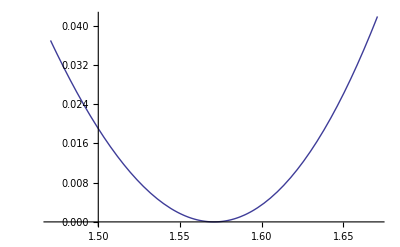

```mathematica
Plot[f[k, 2.0], {k, Pi / 2 - 0.1, Pi / 2 + 0.1}]
```

```mathematica
n := 10
```

```mathematica
Rn[x_] := - 1 / Pi^2 * 1 / x * (- PolyGamma[0.5 + n + x] + PolyGamma[0.5 + n -x])
```

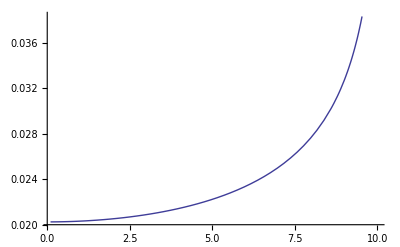

```mathematica
Plot[Rn[x], {x, 0.1, 10}]
```

```mathematica
Sum[1/ (i + 1/2 - x) - 1 / (i + 1/2 + x),{i,n0,Infinity}]
```

-PolyGamma[0,1/2+n0-x]+PolyGamma[0,1/2+n0+x]